```mathematica
(*Quit[]*)
```

# B_c(p1)→χ_cJ(p2, {α,β}) + W_μ(q)

All form factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<MyPackages`HistV2`
```

```mathematica
chiList = {"chi_c0", "chi_c1", "chi_c2"};
```

```mathematica
<<"./funcs.m"
```

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
```

## Intro

```mathematica
gammaTot = (6.6*10^-22 10^-3)/(0.5*10^-12);
```

```mathematica
Clear[getMcc];
(* 1P masses from PDG *)
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
$Vbc = 40.8*10^-3;
$mPi = 0.140GeV;
$a1 = 1.14;
getMcc[out_]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
```

```mathematica
Clear[Ngamma];
Ngamma[out_, outL_, fffit_]:=Module[{
$Mcc=getMcc[out],
$q2=Switch[outL,"P", mPi, "V", mV, "W",q2]
},
gamma[out, outL]//.{
beta -> √(1-((Mcc+√q2)/MBc)^2)√(1-((Mcc-√q2)/MBc)^2),
GF->1.16*10^-5 GeV^-2,fP->130MeV,fV->208MeV,
Vuq ->0.973,Vbc-> 40.8*10^-3,a1 ->$a1
}//.{MBc -> $MBc, mPi->$mPi, mV->775MeV, Mcc->$Mcc, q2->$q2}/.fffit]
Ngamma[out_, "enu", fffit_]:=Ngamma[out,"W", fffit]/.{rhoL[_]->0, rhoT[_]->1/(6 π^2)}
```

```mathematica
Clear[q2Max];
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[BR];
BR::usage="BR[out, outL, ffName] -- my prediction for the branching fraction Bc -> out + outL using FF set ffName (in %)";
Clear[$BR];
$BR::usage="BR[out, outL, ffName] -- prediction for the branching fraction Bc -> out + outL using FF set ffName, presented in the paper (in %)";
```

## Ebert

```mathematica
ffName = "Ebert";
```

```mathematica
<<"./mdat/ebert_ff.mdat";
FFRule = ffFitRule
```

{fPlus(q2_):>0.0000980247 q2^3+0.00176881 q2^2+0.0199961 q2+0.232823,fMinus(q2_):>-0.00128538 q2^3+0.000930923 q2^2-0.0802527 q2-0.690014,hV1(q2_):>-0.000108954 q2^3+0.00333859 q2^2-0.00199503 q2-0.0755446,hV2(q2_):>-0.00248097 q2^3+0.0119635 q2^2-0.0876538 q2-0.361771,hV3(q2_):>0.00342263 q2^3-0.01219 q2^2+0.132895 q2+0.840553,hA(q2_):>-0.00136207 q2^3-0.000760045 q2^2-0.107739 q2-0.93232,tV(q2_):>-0.00343585 q2^3+0.0144402 q2^2-0.122916 q2-0.676794,tA1(q2_):>-0.000254442 q2^3-0.0046253 q2^2-0.0352815 q2-0.517667,tA2(q2_):>-0.00195217 q2^3+0.013911 q2^2-0.0287563 q2+0.0810283,tA3(q2_):>0.}

### Two-Body Decays

```mathematica
Clear[$gamma];
$gamma::usage="$gamma[out, outL, type] is the width of Bc -> out outL decay from tables II, VI (in 10^-15GeV)";
$gamma[out_,outL_]:=$gamma[out,outL,"1P"];
(* Table VI *)
$gamma["chi_c0","P"] = 0.23($a1)^2;
$gamma["chi_c0","V"] = 0.64($a1)^2;
$gamma["chi_c1","P"] = 0.22($a1)^2;
$gamma["chi_c1","V"] = 0.16($a1)^2;
$gamma["chi_c2","P"] = 0.41($a1)^2;
$gamma["chi_c2","V"] = 1.18($a1)^2;
```

```mathematica
$BR["chi_c0", "enu", ffName]=0.087;
$BR["chi_c1", "enu", ffName]=0.082;
$BR["chi_c2", "enu", ffName]=0.16;
$BR["chi_c0", "P", ffName]=0.021; $BR["chi_c0", "V", ffName]=0.058;
$BR["chi_c1", "P", ffName]=0.020; $BR["chi_c1", "V", ffName]=0.015;
$BR["chi_c2", "P", ffName]=0.038; $BR["chi_c2", "V", ffName]=0.11;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P:	 this/Ebert=0.712476	 Br this/Ebert=0.768271

Bc ->chi_c1  P:	 this/Ebert=0.0215416	 Br this/Ebert=0.0233296

Bc ->chi_c2  P:	 this/Ebert=0.745653	 Br this/Ebert=0.792087

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<>":\t this/Ebert=", 10^15 Ngamma[out, outL, ffFitRule]/$gamma[out,outL], "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V:	 this/Ebert=0.503689	 Br this/Ebert=0.547205

Bc ->chi_c1  V:	 this/Ebert=0.58753	 Br this/Ebert=0.617014

Bc ->chi_c2  V:	 this/Ebert=0.52665	 Br this/Ebert=0.556221

### Semileptonic decays

```mathematica
json = Import["../literatute/Ebert_1007.1369/Fig4.json"];
extractNames[json]
```

(1 | chi_c0_e
2 | chi_c0_tau
3 | chi_c1_e
4 | chi_c1_tau
5 | chi_c2_e
6 | chi_c2_tau)

```mathematica
Clear[distEE];
distEE::usage="distEE[out, ffName]";
i=1;
Do[
distEE[out, ffName] = extractFF[json, i]["data"];
distEE[out, ffName] = 100*10^-13($Vbc)^2 HST2D[distEE[out,ffName]]/gammaTot;
i += 2;
,{out, chiList}];
```

```mathematica
Clear[genENuPlot];
genENuPlot::usage = "genENuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu", ffName]=100NIntegrate[Ngamma[out,"enu", ffFitRule],{q2,0,q2Max[out]}]/gammaTot;
Print["Br[this]/Br[Ebert]=",BR[out, "enu", ffName]/$BR[out, "enu", ffName]];
root=readROOT[getFileName[out, "enu", "1"], Norm-> $BR[out, "enu", ffName]];
Show[
PlotHST@NormalizeHST@distEE[out, ffName],
Plot[100*Ngamma[out,"enu", ffFitRule]/gammaTot/BR[out, "enu", ffName], {q2, 0.2,q2Max[out]}],
PlotHST@NormalizeHST@root,
AxesLabel->{"q2, GeV^2", "1/Γ ⅆΓ/ⅆq^2, 1/GeV^2"}, PlotLabel->out, PlotRange->All]
]
```

Br[this]/Br[Ebert]=0.999878

Br[this]/Br[Ebert]=0.98078

Br[this]/Br[Ebert]=0.981686

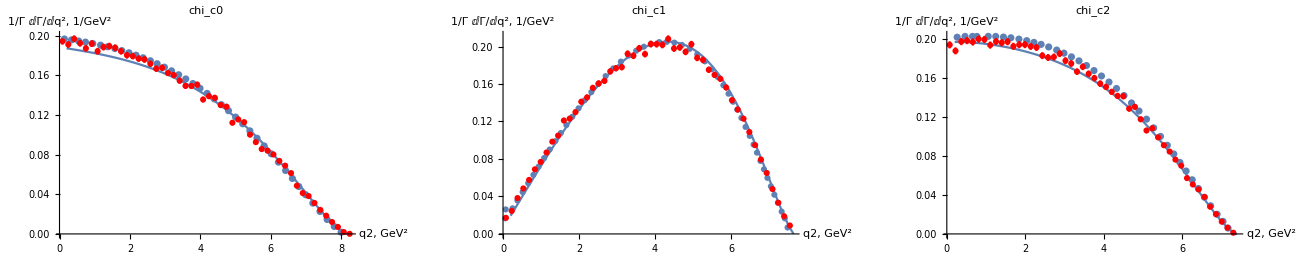

```mathematica
GraphicsGrid[{Table[genENuPlot[out], {out, chiList}]}, ImageSize->1300]
```

### nπ decays

```mathematica
<<"./mdat/rhoT.mdat";
```

```mathematica
Clear[genNPiPlot];
genNPiPlot::usage="genNPiPlot[out, mPi]";
genNPiPlot[out_, nPi_, ffName_]:=Module[{},
mode = ToString[nPi]<>"pi";react= "Bc→"<>out<>" "<>mode;
BR[out, mode,ffName]= NIntegrate[100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}];
Print["Br[",react,"]:=", BR[out, mode,ffName],"%"];
ffNum=Switch[ffName,"Ebert","1","Wang","2"];
root = readROOT[getFileName[out,mode,ffNum],Norm->BR[out, mode,ffName]];
Show[
PlotHST[1.1root],
Plot[100/gammaTot Ngamma[out,"W", FFRule]/.{rhoL[_]->0,rhoT[_]->ConstNπ[nPi]*FqNπ[nPi]},{q2, (nPi*$mPi)^2,q2Max[out]}, PlotRange->All]
,PlotRange->All, PlotLabel->react]
]
```

Br[Bc→chi_c0 2pi]:=0.0428969%

Br[Bc→chi_c1 2pi]:=0.0126569%

Br[Bc→chi_c2 2pi]:=0.0823478%

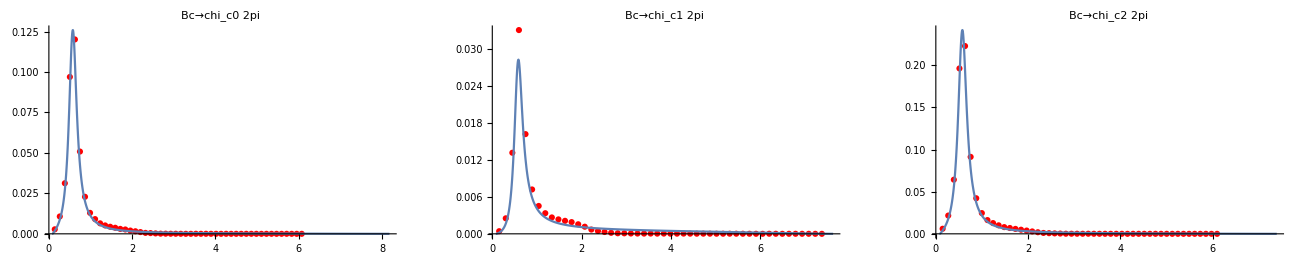

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 3pi]:=0.0267099%

Br[Bc→chi_c1 3pi]:=0.016728%

Br[Bc→chi_c2 3pi]:=0.0515777%

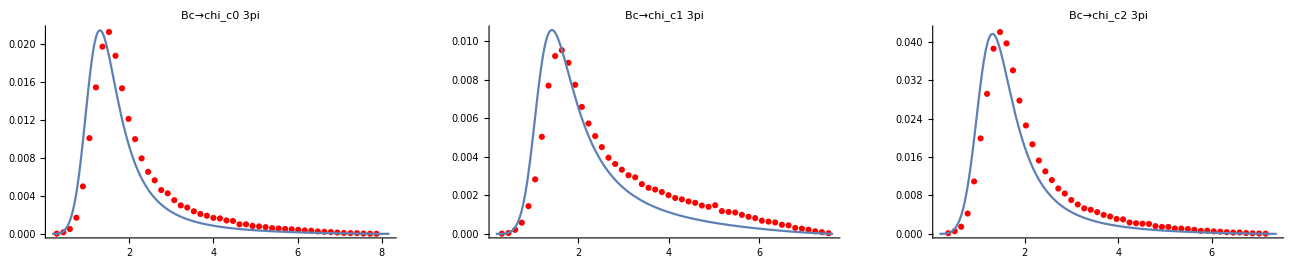

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.0028011%

Br[Bc→chi_c1 5pi]:=0.00351112%

Br[Bc→chi_c2 5pi]:=0.00496707%

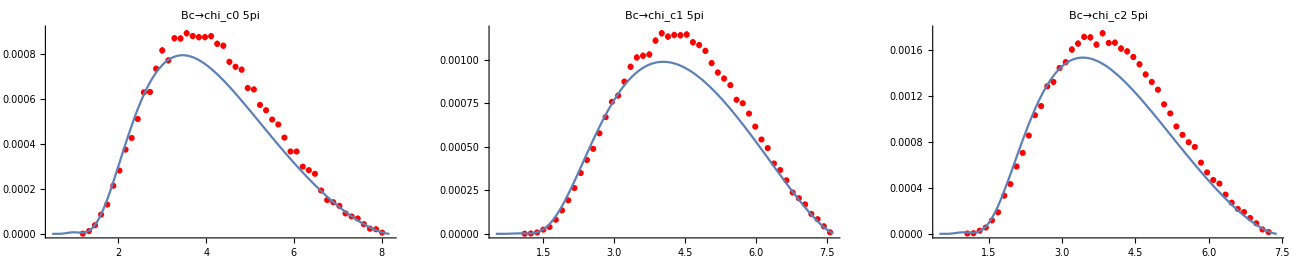

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Wang

```mathematica
ffName = "Wang";
```

```mathematica
<<"./mdat/wang_ff.mdat";
FFRule = ffFitRule$Wang
```

{fPlus(q2_):>-0.000348281 q2^3+0.0018872 q2^2-0.0299383 q2-0.254256,fMinus(q2_):>0.000814326 q2^3-0.00657645 q2^2+0.0659497 q2+0.576102,hV1(q2_):>0.000162205 q2^3-0.000668611 q2^2+0.00756277 q2-0.178867,hV2(q2_):>-0.000414285 q2^3+0.00312312 q2^2-0.0441231 q2-0.520004,hV3(q2_):>0.000520855 q2^3-0.00502003 q2^2+0.0658704 q2+1.09319,hA(q2_):>0.000450084 q2^3-0.00376052 q2^2+0.0659085 q2+0.931121,tV(q2_):>0.000254525 q2^3-0.00225139 q2^2+0.0436616 q2+0.868286,tA1(q2_):>-0.000295842 q2^3+0.00233561 q2^2-0.0294099 q2-0.425225,tA2(q2_):>-0.000524051 q2^3+0.00426751 q2^2-0.0204552 q2-0.125631,tA3(q2_):>0.000146115 q2^3-0.000466823 q2^2+0.0434767 q2+0.577121}

### Two-Body Decays

```mathematica
$BR["chi_c0", "enu", ffName]=0.13±0.03;
$BR["chi_c1", "enu", ffName]=0.11±0.03;
$BR["chi_c2", "enu", ffName]=0.10±0.03;
$BR["chi_c0", "P", ffName]=0.031±0.004; $BR["chi_c0", "V", ffName]=0.076±0.009;
$BR["chi_c1", "P", ffName]=0.0021±0.0002; $BR["chi_c1", "V", ffName]=0.023±0.002;
$BR["chi_c2", "P", ffName]=0.021±0.005; $BR["chi_c2", "V", ffName]=0.056±0.011;
```

```mathematica
outL="P";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  P	 Br this/Ebert=0.630367±0.0813377

Bc ->chi_c1  P	 Br this/Ebert=0.702635±0.0669176

Bc ->chi_c2  P	 Br this/Ebert=0.61583±0.146626

```mathematica
outL="V";
Do[
BR[out, outL, ffName]=10^2 Ngamma[out, outL, FFRule]/gammaTot;
Print["Bc ->"<> out" "<>outL<> "\t Br this/Ebert=", BR[out, outL,ffName]/$BR[out, outL, ffName]]
,{out, chiList}]
```

Bc ->chi_c0  V	 Br this/Ebert=0.513123±0.0607646

Bc ->chi_c1  V	 Br this/Ebert=0.580496±0.0504779

Bc ->chi_c2  V	 Br this/Ebert=0.509136±0.100009

### Semileptonic decays

```mathematica
Clear[extractNames];
extractNames[json_]:=Module[{names = json⟦3,2,All,1,2⟧}, Table[{i,names⟦i⟧},{i,Length[names]}]];
```

```mathematica
json = Import["../literatute/1107.0474/Fig5_e.json"];
names = extractNames[json]
```

(1 | chi_c0
2 | chi_c1
3 | chi_c2)

```mathematica
Clear[genEnuPlot]
genEnuPlot::usage="genEnuPlot[out]";
genENuPlot[out_]:=Module[{},
BR[out, "enu",ffName] = NIntegrate[100/gammaTot Ngamma[out,"enu", FFRule],{q2, 0, q2Max[out]}] ;
root = readROOT[getFileName[out,"enu","2",Var->"m2_0m1"], Norm->1];
PlotQ2 = Show[
Plot[100/gammaTot Ngamma[out,"enu", FFRule]/BR[out, "enu",ffName], {q2, 0.2,q2Max[out]}],
PlotHST[root]
, AxesLabel->{"q2, GeV^2", "~ⅆΓ/dq2"}, PlotLabel->"Bc -> "<>out<>"e nu"];
pap =NormalizeHST@HST2D[extractFF[json, Select[names, #⟦2⟧==out&][[1,1]]]["data"]];
root = readROOT[getFileName[out,"enu","2",Var->"e_2"], Norm->1];
PlotEE = Show[
PlotHST[pap, Joined->True], PlotHST[root]
,AxesLabel->{"Ee, GeV", "1/Γ ⅆΓ/ⅆEe"}, PlotLabel->"Bc -> "<>out<>"e nu"];
Print["Br[Bc->"<>out<>"+enu]=",BR[out, "enu",ffName],"\t this/Wang=",BR[out, "enu",ffName]/$BR[out, "enu",ffName]];
GraphicsGrid[{{PlotQ2, PlotEE}}, ImageSize->1000]
];
```

Br[Bc->chi_c0+enu]=0.0999882	 this/Wang=0.76914±0.177494

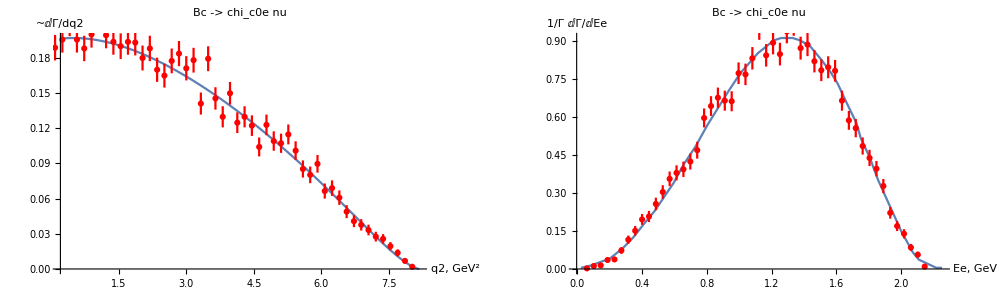

```mathematica
genENuPlot["chi_c0"]
```

Br[Bc->chi_c1+enu]=0.0798413	 this/Wang=0.72583±0.197954

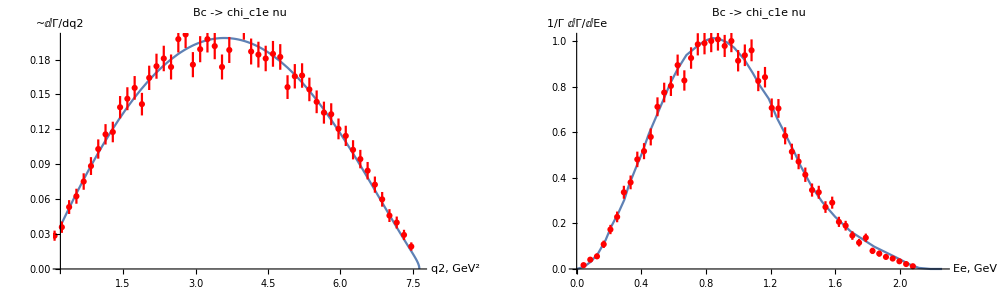

```mathematica
genENuPlot["chi_c1"]
```

Br[Bc->chi_c2+enu]=0.0700048	 this/Wang=0.700048±0.210015

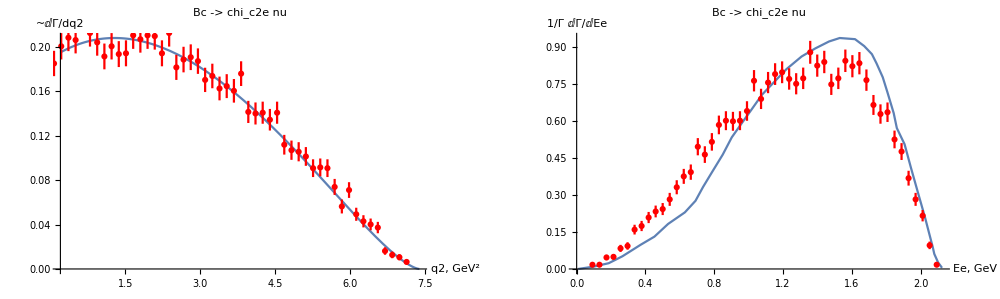

```mathematica
genENuPlot["chi_c2"]
```

### nπ decays

Br[Bc→chi_c0 2pi]:=0.0523452%

Br[Bc→chi_c1 2pi]:=0.0175659%

Br[Bc→chi_c2 2pi]:=0.0379225%

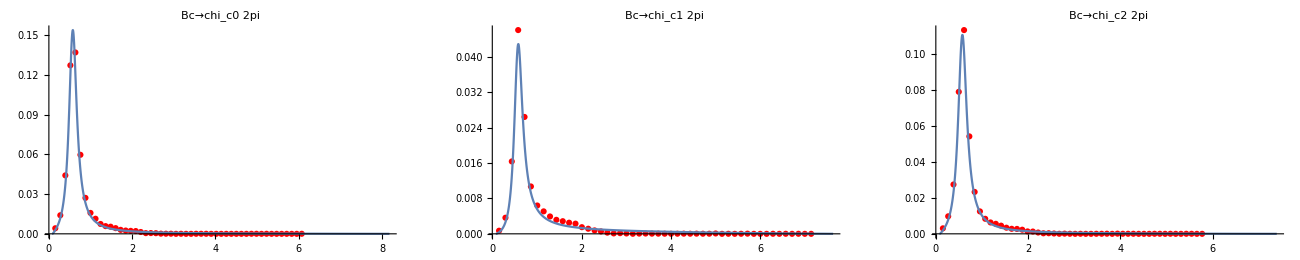

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 2, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 3pi]:=0.032379%

Br[Bc→chi_c1 3pi]:=0.0199618%

Br[Bc→chi_c2 3pi]:=0.0244721%

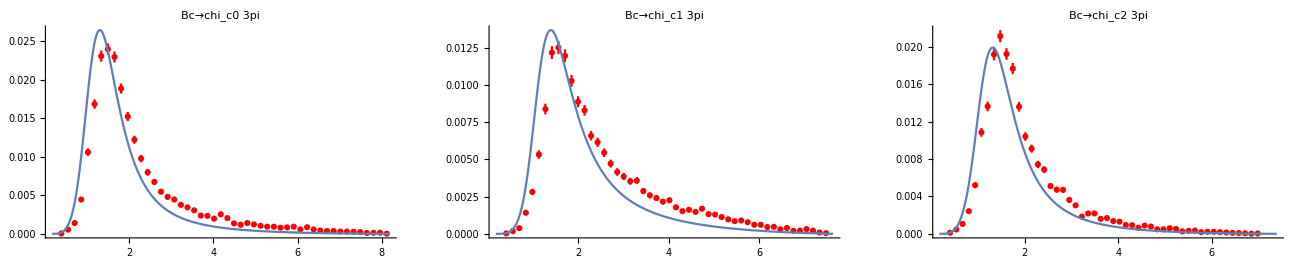

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 3, ffName],{out,chiList}]}, ImageSize->1300]
```

Br[Bc→chi_c0 5pi]:=0.00310919%

Br[Bc→chi_c1 5pi]:=0.00328885%

Br[Bc→chi_c2 5pi]:=0.00214886%

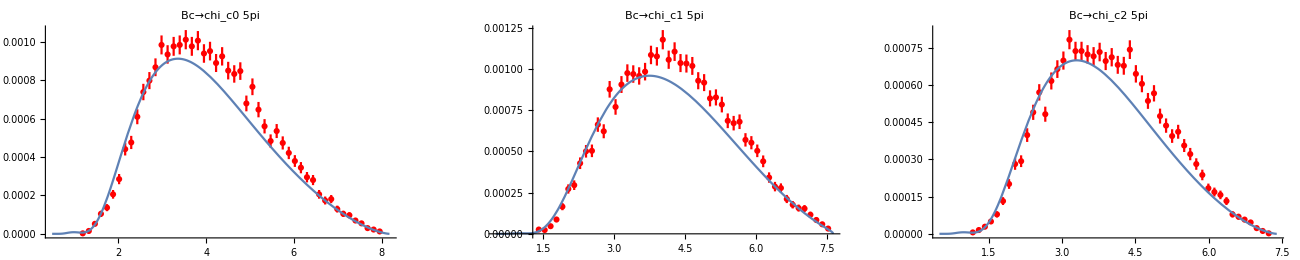

```mathematica
GraphicsGrid[{Table[genNPiPlot[out, 5, ffName],{out,chiList}]}, ImageSize->1300]
```

## Saving

```mathematica
<<"funcs.m"
```

```mathematica
SaveVar["./mdat/branchings.mdat", BR];
SaveVar["./mdat/branchings.mdat", $BR, Overwrite->False];
```

## Combined Tables

```mathematica
tab = Table[
Flatten[Table[BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V","2pi", "3pi", "5pi"}}];
tab = Round[tab,0.0001];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Predictions Table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V","2pi", "3pi", "5pi"}}]
,Dividers->{{2->True, 4->True, 6->True}, {2->True}}, Alignment->Right]
]
```

Predictions Table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.087 | 0.1 | 0.0804 | 0.0798 | 0.1571 | 0.07
P | 0.0161 | 0.0195 | 0.0005 | 0.0015 | 0.0301 | 0.0129
V | 0.0317 | 0.039 | 0.0093 | 0.0134 | 0.0612 | 0.0285
2pi | 0.0429 | 0.0523 | 0.0127 | 0.0176 | 0.0823 | 0.0379
3pi | 0.0267 | 0.0324 | 0.0167 | 0.02 | 0.0516 | 0.0245
5pi | 0.0028 | 0.0031 | 0.0035 | 0.0033 | 0.005 | 0.0021

```mathematica
tab = Table[
Flatten[Table[$BR[out,outL, ffName],{out, chiList},{ffName,{"Ebert","Wang"}}]]
,{outL,{"enu","P","V"}}];
colNames = Flatten[Table[out<>" ["<>ffName<>"]",{out, chiList},{ffName,{"Ebert","Wang"}}]];
Print["Papers' table\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{None, {2->True}}, Alignment->Right]
]
```

Papers' table
  | chi_c0 [Ebert] | chi_c0 [Wang] | chi_c1 [Ebert] | chi_c1 [Wang] | chi_c2 [Ebert] | chi_c2 [Wang]
enu | 0.087 | 0.13±0.03 | 0.082 | 0.11±0.03 | 0.16 | 0.1±0.03
P | 0.021 | 0.031±0.004 | 0.02 | 0.0021±0.0002 | 0.038 | 0.021±0.005
V | 0.058 | 0.076±0.009 | 0.015 | 0.023±0.002 | 0.11 | 0.056±0.011

```mathematica
ffName="Ebert";
tab = Table[
Flatten[Table[{BR[out,outL, ffName], $BR[out, outL, ffName],BR[out,outL, ffName]/$BR[out, outL, ffName]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
tab = Round[tab,0.0001];
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Ebert
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.087 | 0.087 | 0.9999 | 0.0804 | 0.082 | 0.9808 | 0.1571 | 0.16 | 0.9817
P | 0.0161 | 0.021 | 0.7683 | 0.0005 | 0.02 | 0.0233 | 0.0301 | 0.038 | 0.7921
V | 0.0317 | 0.058 | 0.5472 | 0.0093 | 0.015 | 0.617 | 0.0612 | 0.11 | 0.5562

```mathematica
Clear[RemoveError];
RemoveError[a_]:=a;
RemoveError[a_±b_]:=a
```

```mathematica
ffName="Wang";
tab = Table[
Flatten[Table[{BR[out,outL, ffName], RemoveError[$BR[out, outL, ffName]],RemoveError[BR[out,outL, ffName]/$BR[out, outL, ffName]]},{out, chiList}]]
,{outL,{"enu","P","V"}}];
(*tab = Round[tab,0.001];*)
colNames = Flatten[Table[{"this","work","this/work"},{out, chiList}]];
Print["Comparison:",ffName,"\n",
Grid[
MapThread[Prepend, {Prepend[tab, colNames],{" ","enu","P","V"}}]
,Dividers->{{5->True,8->True}, {2->True}}, Alignment->Right]
]
```

Comparison:Wang
  | this | work | this/work | this | work | this/work | this | work | this/work
enu | 0.0999882 | 0.13 | 0.76914 | 0.0798413 | 0.11 | 0.72583 | 0.0700048 | 0.1 | 0.700048
P | 0.0195414 | 0.031 | 0.630367 | 0.00147553 | 0.0021 | 0.702635 | 0.0129324 | 0.021 | 0.61583
V | 0.0389973 | 0.076 | 0.513123 | 0.0133514 | 0.023 | 0.580496 | 0.0285116 | 0.056 | 0.509136